```mathematica
Tanh[Log[1-t^2]]
```

(-1+(1-t^2)^2)/(1+(1-t^2)^2)

```mathematica
S[t_]:=Tanh[Log[RiemannSiegelZ[t]]]
```

```mathematica
S[t]
```

(-1+(1-t^2)^2)/(1+(1-t^2)^2)

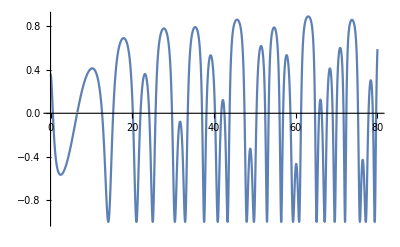

```mathematica
Plot[S[t],{t,0,80}]
```

```mathematica
Solve[S[t]==0,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→S^(-1)[0]}}

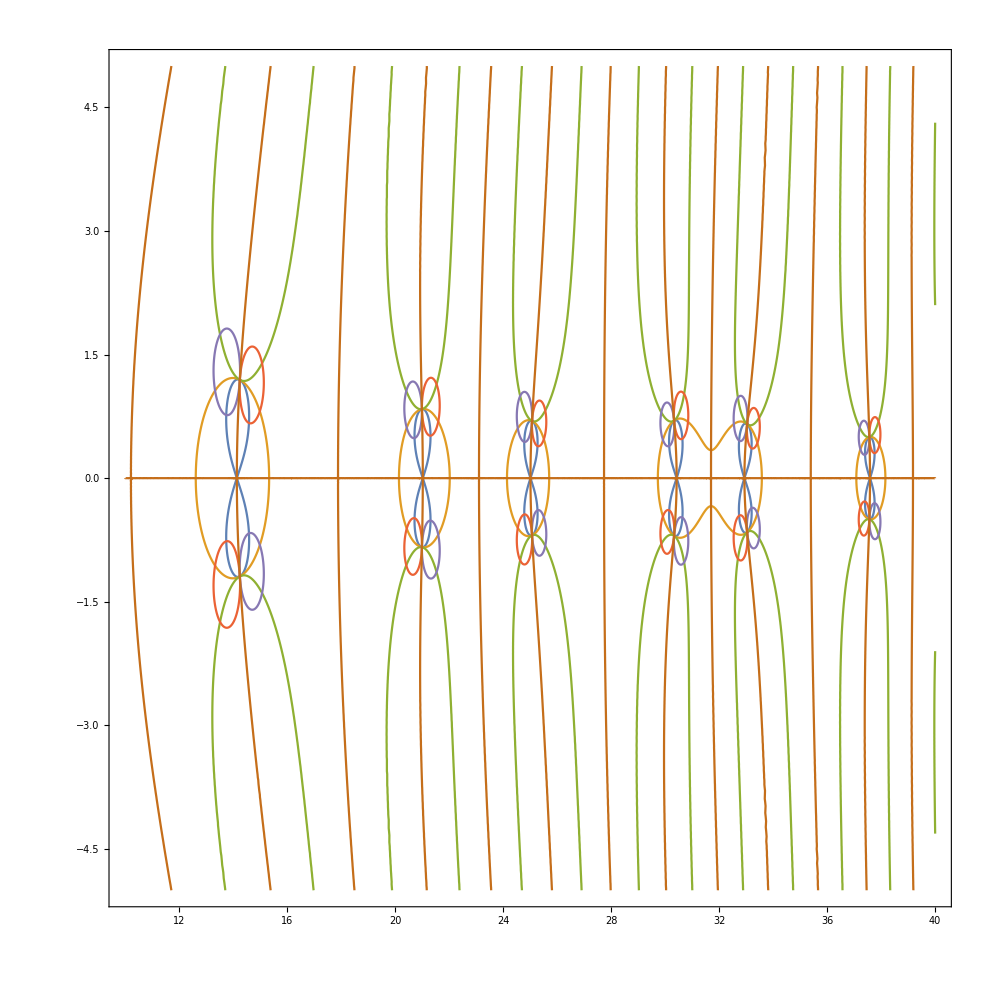

```mathematica
ContourPlot[{Re[S[x+I*y]]==-1,Re[S[x+I*y]]==0,Re[S[x+I*y]]==1,Im[S[x+I*y]]==1,Im[S[x+I*y]]==-1,Im[S[x+I*y]]==0},{x,10,40},{y,-5,5},PerformanceGoal->"HighQuality",MaxRecursion->5]
```

```mathematica
·
```

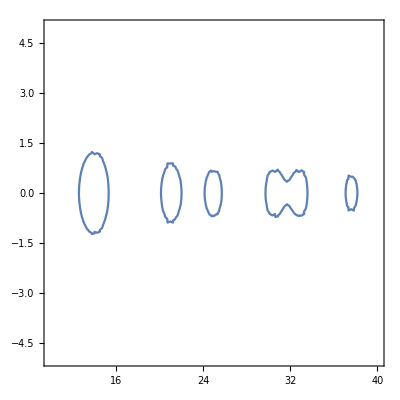

```mathematica
ContourPlot[{},{x,10,40},{y,-5,5},PerformanceGoal->"HighQuality"]
```

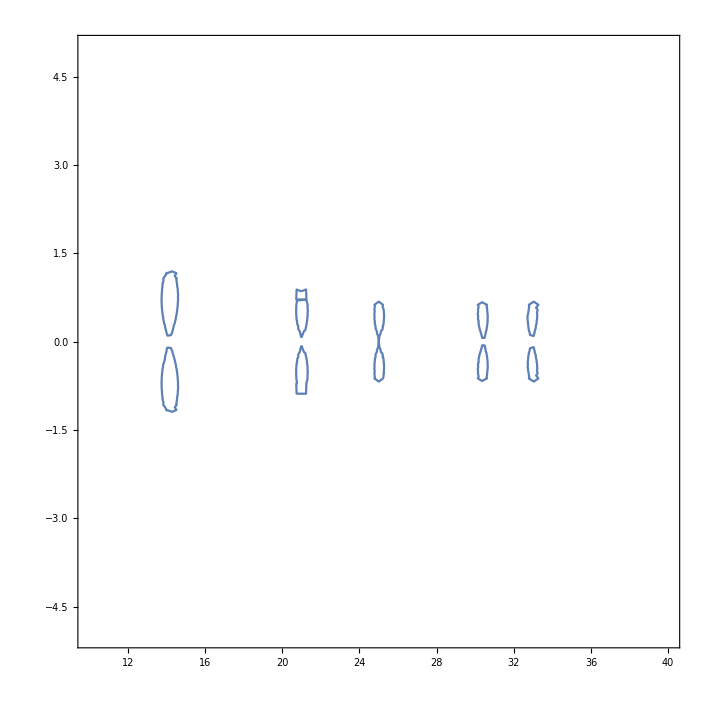

```mathematica
ContourPlot
```

```mathematica
ContourPlot[Re[S[x+I*y]]==0,{x,-2,2},{y,-2,2},PerformanceGoal->"Quality"]
```

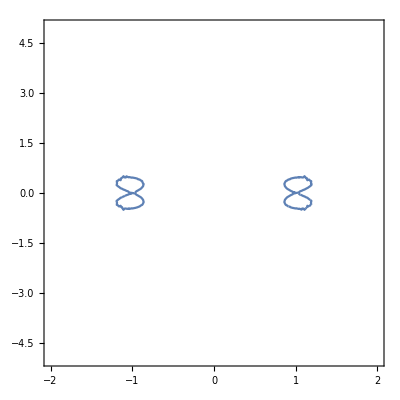
```mathematica
-Graphics--Graphics-
```